### Plot Options

Set all of the options for the different types of plots used throughout the program here. I have tried to keep a consistent style for all plots.

```mathematica
(* Include the Needs["ErrorBarPlots"] command to include the ErrorListPlot function*)
Needs["ErrorBarPlots`"]
```

```mathematica
SetOptions[ListPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,Joined->True,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[ErrorListPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,Joined->True,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[ListLogPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,Joined->True,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[Plot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[LogLogPlot,{AspectRatio->0.4,PlotStyle->{Red,Green,Blue,Black},Frame->True,FrameStyle->Thick,Axes->False,BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,GridLines->None,PlotRange->All,FrameLabel->{"x","y"}}];
```

```mathematica
SetOptions[ArrayPlot,{BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,DataReversed->True,FrameTicks->Automatic,ColorFunction->"SunsetColors"}];
```

```mathematica
SetOptions[ListPlot3D,{BaseStyle->{FontFamily->"Helvetica",FontSize->18},ImageSize->500,PlotRange->All}];
```

### Compiler

Set the options for the compiler in this section, such as how many iterations before compiling basic functions.

```mathematica
Cases["CompileOptions"/.SystemOptions["CompileOptions"],opt:(s_String->_)/;StringMatchQ[s,__~~"Length"]]
SetSystemOptions["CompileOptions"->{"FoldCompileLength"->2,"TableCompileLength"->2,"NestCompileLength"->100,"MapCompileLength"->2,"ListableFunctionCompileLength"->2}]
```

{ApplyCompileLength→∞,ArrayCompileLength→250,FoldCompileLength→100,ListableFunctionCompileLength→250,MapCompileLength→100,NestCompileLength→100,ProductCompileLength→250,SumCompileLength→250,TableCompileLength→250}

CompileOptions→{ApplyCompileLength→∞,ArrayCompileLength→250,AutoCompileAllowCoercion→False,AutoCompileProtectValues→False,AutomaticCompile→False,BinaryTensorArithmetic→False,CompileAllowCoercion→True,CompileConfirmInitializedVariables→True,CompiledFunctionArgumentCoercionTolerance→2.10721,CompiledFunctionMaxFailures→3,CompileDynamicScoping→False,CompileEvaluateConstants→True,CompileOptimizeRegisters→False,CompileParallelizationThreshold→10,CompileReportCoercion→False,CompileReportExternal→False,CompileReportFailure→False,CompileValuesLast→True,FoldCompileLength→2,InternalCompileMessages→False,ListableFunctionCompileLength→2,MapCompileLength→2,NestCompileLength→100,NumericalAllowExternal→False,ProductCompileLength→250,ReuseTensorRegisters→True,SumCompileLength→250,SystemCompileOptimizations→All,TableCompileLength→2}

```mathematica
Compile`CompilerFunctions[]//Sort
```

{Abs,AddTo,And,Append,AppendTo,Apply,ArcCos,ArcCosh,ArcCot,ArcCoth,ArcCsc,ArcCsch,ArcSec,ArcSech,ArcSin,ArcSinh,ArcTan,ArcTanh,Arg,Array,ArrayDepth,Internal`Bag,Internal`BagPart,BitAnd,BitNot,BitOr,BitXor,Block,BlockRandom,Boole,Break,Cases,Catch,Ceiling,Chop,Internal`CompileError,System`Private`CompileSymbol,Complement,ComposeList,CompoundExpression,Conjugate,ConjugateTranspose,Continue,Cos,Cosh,Cot,Coth,Count,Csc,Csch,Decrement,Delete,DeleteCases,Dimensions,Divide,DivideBy,Do,Dot,Drop,Equal,Erf,Erfc,EvenQ,Exp,Internal`Expm1,Fibonacci,First,FixedPoint,FixedPointList,Flatten,NDSolve`FEM`FlattenAll,Floor,Fold,FoldList,For,FractionalPart,FreeQ,Gamma,Compile`GetElement,Goto,Greater,GreaterEqual,Gudermannian,Haversine,If,Im,Implies,Increment,Indexed,Inequality,Compile`InnerDo,Insert,IntegerDigits,IntegerPart,Intersection,InverseGudermannian,InverseHaversine,Compile`IteratorCount,Join,Label,Last,Length,Less,LessEqual,List,Log,Log10,Internal`Log1p,Log2,LogGamma,LogisticSigmoid,LucasL,Map,MapAll,MapAt,MapIndexed,MapThread,NDSolve`FEM`MapThreadDot,MatrixQ,Max,MemberQ,Min,Minus,Mod,Compile`Mod1,Module,Most,N,Negative,Nest,NestList,NonNegative,Not,OddQ,Or,OrderedQ,Out,Outer,Part,Partition,Piecewise,Plus,Position,Positive,Power,PreDecrement,PreIncrement,Prepend,PrependTo,Product,Quotient,Ramp,Random,RandomChoice,RandomComplex,RandomInteger,RandomReal,RandomSample,RandomVariate,Range,Re,RealAbs,RealSign,Internal`ReciprocalSqrt,ReplacePart,Rest,Return,Reverse,RotateLeft,RotateRight,Round,RuleCondition,SameQ,Scan,Sec,Sech,SeedRandom,Select,Set,SetDelayed,Compile`SetIterate,Sign,Sin,Sinc,Sinh,Sort,Sqrt,Internal`Square,Internal`StuffBag,Subtract,SubtractFrom,Sum,Switch,Table,Take,Tan,Tanh,TensorRank,Throw,Times,TimesBy,Tr,Transpose,Unequal,Union,Unitize,UnitStep,UnsameQ,VectorQ,Which,While,With,Xor}

```mathematica
Needs["CompiledFunctionTools`"]
```

Test if a function is ' well' compiled (i.e. there are no calls to MainEvaluate)

```mathematica
FastCompiledFunctionQ[function_CompiledFunction]:=(StringFreeQ[CompiledFunctionTools`CompilePrint@function,"MainEvaluate"])
```

### Moments

Calculate the moments of a distribution.
The getMoment functions are passed in the distribution and an order (either 1 or 2), passing in a 1 returns the mean of the distribution (first moment), passing in a 2 returns the variance (second moment).
As before there are two versions of the function, 1D and 2D, both do the same thing but take either a 1D list or 2D list as arguements.

```mathematica
Clear[getMoment1D];
getMoment1D=
With[{},
Compile[
{{data,_Real,1},{order,_Integer}},
Block[{data2=Transpose[{Range@Length@data,data}],norm,mean},
norm=Total@data2⟦All,2⟧;

mean=N@Total[(#⟦1⟧#⟦2⟧&/@data2)/norm];
If[order==1,mean,N@Total[((#⟦1⟧-mean)^order#⟦2⟧&/@data2)/norm]]
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[getMoment1D];
FastCompiledFunctionQ[getMoment1D]
```

True

```mathematica
Clear[getMoment2D];
getMoment2D=
With[{},
Compile[
{{data2,_Real,2},{order,_Integer}},
Block[{norm,mean},
norm=Total@data2⟦All,2⟧;

mean=N@Total[(#⟦1⟧#⟦2⟧&/@data2)/norm];
If[order==1,mean,N@Total[((#⟦1⟧-mean)^order#⟦2⟧&/@data2)/norm]]
],
RuntimeAttributes->{Listable},Parallelization->True,"RuntimeOptions"->{"EvaluateSymbolically"->False},CompilationOptions->{"InlineCompiledFunctions"->True,"ExpressionOptimization"->True},CompilationTarget->"MVM"
]
];
CompilePrint[getMoment2D];
FastCompiledFunctionQ[getMoment2D]
```

True

```mathematica
(*getMoment decides whether to call the 1D or 2D version of the getMoment function depedning on the dimensions of the arguements. It also test that there are no negative values ion the distribution as this can throw off the moments calculation*)
```

```mathematica
(*fit1DN is passed the data and a list of the estimates as arguements, it can also be passed an accuracy goal and the max number of iterations although these are set to a default of 4 and 100respectively. The function will fit the equation of a 1D Normal distribution to the data;the fit parameters and residuals can then be extracted from this function.*)
Clear[fit1DN];
fit1DN[data_,guess_List,AG_:4,MI_:100]:=Module[{μ,σ,x1,Bg,A ,σx,m,μx,BgGuess,AGuess, μGuess,σGuess},
(*If thinking of this as a probability distribution it's best to get rid of "negative" probabilities 
and shift everything to the zero line, remember this only to get approx numebrs for cutting the data
μAndσ=getMeanSigma[shiftToZeroLine[data]]*)
{BgGuess,AGuess, μGuess,σGuess}=guess;
(*
Different methods, 
NonlinearModelFitMethods={"Newton","Gradient","ConjugateGradient","LevenbergMarquardt"};
NMinimizeMethods={"RandomSearch","DifferentialEvolution","SimulatedAnnealing","NelderMead"};*)
NonlinearModelFit[data,Bg+A Exp[-(x1-μx)^2/(2 σx^2) ],{{Bg,BgGuess},{A,AGuess},{μx,μGuess},{σx,σGuess}},x1,AccuracyGoal->AG,MaxIterations->MI,Method->{NMinimize,Method->"DifferentialEvolution"}]
]
```

```mathematica
(*plot1DFit plots overlays a 1D Normal funcitondefined by given parameters over a set of data passed to it.*)
plot1DFit[data_,fitRules_,PlotTitle_,AxisLabel_List]:=Module[{Bg,A,μ,σ},
{Bg,A,μ,σ}=fitRules⟦All,2⟧;
Print@Show[{ListPlot[data,Joined->False,ImageSize->400,PlotLabel -> PlotTitle,Frame -> True,FrameLabel->AxisLabel],Plot[Bg+A Exp[-(x-μ)^2/(2 σ^2) ],{x,0,Length@data},PlotStyle->Red]}]
]
```

## Work

to help go through the python implmentatino of Andy Wolski' s matlab code

```mathematica
SetDirectory["\\\\fed.cclrc.ac.uk\\org\\NLab\\ASTeC\\Projects\\VELA\\Work\\2019\\03\\04\\10pC degaussing, sol -125.0"]
```

\\fed.cclrc.ac.uk\org\NLab\ASTeC\Projects\VELA\Work\2019\03\04\10pC degaussing, sol -125.0

```mathematica
beamFN="S02-CAM-03_2019-3-4_17-49-55_10images.hdf5";
backFN="S02-CAM-03_2019-3-4_17-50-13_1images.hdf5";
```

```mathematica
beamdataRaw=Import[beamFN,#]&/@Import[beamFN];
backdataRaw=Import[backFN,#]&/@Import[backFN];
```

```mathematica
Print[backdataRaw⟦1,1⟧⟦1;;3⟧,backdataRaw⟦1,1⟧⟦-3;;-1⟧]
Print[backdataRaw⟦1,2⟧⟦1;;3⟧,backdataRaw⟦1,2⟧⟦-3;;-1⟧]
```

{0,100,96}{98,88,112}

{0,92,97}{92,94,101}

```mathematica
Block[{a},
beamdata=Table[
(* subtract the background image *)
a=beamdataRaw⟦i⟧-backdataRaw⟦1⟧;
Print[a⟦1⟧⟦1;;3⟧,a⟦1⟧⟦-3;;-1⟧];
(* crop the first 50 columsn (this is where the timestamp is imprinted on the image ) *)
#⟦50;;-1⟧&/@a
,{i,1,10}];
]
```

{0,0,1}{-6,14,-11}

{0,-4,-4}{-1,9,-7}

{0,0,1}{-4,9,-7}

{0,-4,3}{5,5,-4}

{0,-2,-4}{0,7,-6}

{0,-4,-5}{-3,3,-7}

{0,1,-2}{11,3,-5}

{0,-6,-2}{-2,9,-10}

{0,-4,1}{-2,9,-7}

{0,-6,-2}{2,7,-7}

```mathematica
Length@beamdata⟦1⟧
Length@beamdata⟦1,1⟧
```

2560

2111

```mathematica
sumrows=(Total/@beamdata⟦1⟧);
sumcols=Total/@Transpose@beamdata⟦1⟧;
```

```mathematica
mean=N@(Total[sumcols Range@Length@sumcols]/(Length@sumcols))
N@(Total[sumcols (Range@Length@sumcols-mean)^2]/(Length@sumcols))
getMoment1D[sumcols,1]
√getMoment1D[sumcols,2]
```

2.60217×10^6

1.67737×10^16

1049.61

310.768

{Bg→663.925,A→73086.,μ→1042.5,σ→-20.917}

General::munfl: Exp[-1241.89] is too small to represent as a normalized machine number; precision may be lost.

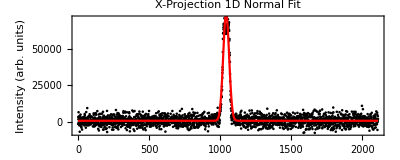

```mathematica
xFit=fit1DN[sumcols,{0,25000, getMoment1D[sumcols,1],√getMoment1D[sumcols,2]}];
xProjFitParam =Join[{Bg->#⟦1⟧,A->#⟦2⟧,μ->#⟦3⟧,σ->#⟦4⟧}&/@{xFit["BestFitParameters"]⟦All,2⟧}]⟦1⟧
plot1DFit[sumcols,xProjFitParam,"X-Projection 1D Normal Fit",{"Pixels","Intensity (arb. units)"}]
```

```mathematica
fit1DN[sumcols,{0,25000, getMoment1D[sumcols,1],getMoment1D[sumcols,2]}]
```

FittedModel[663.925+73086. ⅇ^(-0.0011428 (-1042.5+«8»)^2)]

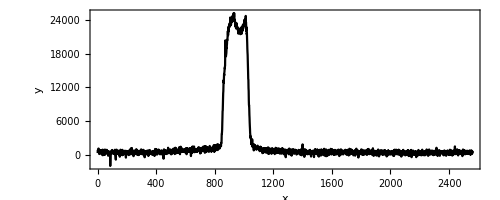

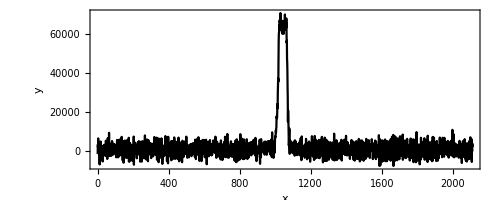

```mathematica
ListPlot[Total/@beamdata⟦1⟧]
ListPlot[Total/@Transpose@beamdata⟦1⟧]
```

```mathematica
MatrixPlot[beamdata⟦1⟧]
```

-Graphics-

```mathematica
MatrixPlot[beamdata⟦1⟧]
```

-Graphics-

```mathematica
pydata={82049568,48696579,71632488,37427538,77266483,45485100,55511079,78248919,91289183,88668205,44306302,125297998,58001192,45157868,81263531,87816100,75496777,36508442,91616612,52759046,70058357,54986969,99545932,103608429,49744439,79166280,51972606,69533952,112782132,56231828,85522716,82246262,66847503,73793258,58525125,47582264,70582061,78839024,60556642,64488267,57345669,67633452,87685093,45223215,90043910,57738893,35591371,41226612,55642253,50924213,72220687,78838856,62129155,76807561,103542829,51186255,84081020,28645845,90306311,65077833,84211977,55052175,90568549,58983790,18097288,69730450,83425771,49285989,92665426,47320106,78446012,74448425,68550787,58590812,42798784,89781991,43978085,45878420,86243376,87750513,76610837,35394559,67436997,47385905,65012487,78445746,75890030,50137790,43585185,85457180,61146221,67961442,43781509,63767385,66650575,80215192,73989793,70123712,46730457,70451184,61605075,75824401,70516774,59442724,95744938,68223352,66322845,59180592,97121254,30021174,38670965,84146725,83163776,75038525,51579669,98497412,54855914,64553778,93713736,31200799,58001203,48761524,86112668,88864529,31921942,55707352,36508339,75562752,89978847,81722075,67306061,83491266,79625208,60032642,73269041,23927913,66388547,70713236,53938402,81787552,85326315,108653867,77331888,61277179,37425975,92468651,117303486,56035272,48892971,50268772,90633730,86636913,33101043,53807286,59246216,97055514,45747354,84212015,82442816,75758977,58066660,34739464,89781852,71172049,98234960,76086714,88733547,89651163,33363357,81525774,71565172,64619550,49482535,58001031,60818864,26024587,113699618,87750693,44961513,111471413,51579761,77004102,41422886,87160926,59770471,102625506,62391660,78576610,98300608,46468216,83163661,64815777,71040832,76414348,50072468,110161060,47778783,51382939,72875660,59966714,76676490,107736667,89192186,23862521,124511403,45420039,75300253,63571008,73006864,50006655,40046832,74383008,83557104,77266321,67306134,73924468,53807194,74841706,80477209,69271796,102494600,63636385,48237707,65667783,85588557,75366023,38408536,63308862,66585584,61342875,50923848,79297431,33887213,50137892,77200844,66650893,90175413,64488343,47123477,114223844,55248767,38867579,62719070,102297815,56494193,87030138,83098286,90502794,113961704,35853055,62981073,75562593,55052097,55510884,36311911,61080982,42864230,77528421,64226338,84539685,100135359,55642294,57017720,65733190,99742505,46664910,21962566,73989854,81525597,102691044,78576898,61670632,38605494,57542433,106163998,73138020,55052091,30611262,104001761,78445786,49744716,92992985,45485652,111995821,55707802,31200814,78969949,88209511,59311651,39326255,57280272,48827105,66126508,58656163,42143650,69992726,77724829,76479809,69402832,44502896,51251827,100004337,45223227,52824629,82835865,68813170,73006948,84277720,56493915,74317599,57084045,57280359,93975894,55052288,45944690,81787687,79166451,84343386,31266860,25762853,51120824,55642110,77659480,60425623,69599239,63702073,90503175,49417006,63243373,67961468,28186724,70254609,26811086,62915779,107736720,59966670,59115044,44699262,70254878,61998324,71106649,90896204,95483088,117107146,28252448,57280293,66060938,69927070,90109697,77593922,100725335,56559657,92010039,69010115,77528548,69861557,96662524,48761673,58722161,30480738,32118419,45354616,75627756,97842224,122349157,88996054,104853461,60098069,70909997,81525337,50727644,69009843,83622716,66060863,76479851,91485742,68419991,58525201,84867447,60753237,63964383,23731712,58721999,85588171,62456941,78183407,67502679,85457231,26417972,68485578,113765316,89847704,68878678,49679150,78248945,49810556,119269251,25697416,71237852,72614040,61211843,62981037,74841605,69402956,45026641,63243046,68616599,58394409,93779277,82246257,59507952,41095344,83491189,37032828,39653887,105704846,80935718,81525267,35525634,65602124,72154844,72745009,51186346,42733074,92206711,50400040,94565734,35918828,103477392,76152136,63964258,26090312,31856038,96793559,55642201,94761829,61211736,75693541,103477350,65143516,76479573,56821655,91419938,38081085,43061120,80804927,71434145,83622460,88471521,68026759,45419861,50727715,106622902,56362890,53676457,26942175,93320581,75103741,43257686,112257926,48171990,43781671,55904337,51120716,86570981,45092583,58001283,69533949,85588245,59966839,107147021,37556743,57476930,50268905,60229169,116582826,50137808,35853505,34870330,90503070,67895934,74382695,61801531,96138241,86177961,80083900,79232034,50530969,75431433,42536765,68092341,64946987,49089300,83163754,35001388,82836140,50596632,46272020,81001224,24583358,85522860,57673547,85719157,75562529,50596525,99807921,64946965,87619456,58656403,70910078,70189123,56166144,74972678,49744726,95679363,68813463,60425504,86177929,48499662,65405806,72220815,48172191,45288879,84212319,83819141,48630956,63308716,59770444,91289056,88405737,58001215,66912803,61670503,79363098,51382899,42405810,76021398,59377121,62391200,80870163,74186283,49023961,44109636,83622477,74055385,52365787,45944413,94434455,70189257,32118487,50203730,53938403,95614160,104919034,58459861,54724487,80935917,68157858,52955479,64357415,59573731,86833378,30218452,50465478,78773526,71631246,85260954,27073454,61998195,56166568,52824523,98366144,39784969,109964387,52431656,92665321,74972661,49482615,50858650,37360532,73989699,78970061,36377660,46206673,55838918,111668234,63964049,61277336,41160885,84146786,85326346,34281047,69534003,56363013,82836106,63374479,75038445,55183615,34936401,83294770,53807549,78904304,62587852,96727947,71106856,44830333,95351969,82639527,74055285,92665284,34018956,87095696,81459896,40309458,122152366,48237771,58983912,56952667,76807509,79363270,55249216,84277760,75693716,40309368,45223787,95876502,89978634,45616645,52889927,83753469,84277576,86046977,33953279,72220587,75628042,68681933,68944451,45420209,61539795,88340529,66192027,89323408,57739194,71892862,87422982,69861805,70385666,67764617,65209201,68747702,59180731,34149703,71237457,61670682,51120645,50924510,59246156,73531231,56559520,80477265,47189459,70123542,62915740,25500867,57477085,74448480,71499834,60688007,98300531,66257736,69009948,54659237,40047247,50858698,47123871,43716185,76479725,59049470,79428738,74121097,93648178,47189525,54790531,85129689,46730697,75496993,50269391,88995669,93517075,43847392,55511477,82311923,106032958,55904380,37360983,79101133,95155486,79756399,68092615,80018612,47910295,105967261,78052718,82705048,106098477,66519931,82901815,63243409,96728008,55314790,67830479,74841862,39850521,75497120,76807619,63177943,92403161,28056739,45682221,60556745,82246469,94696400,85653888,49613957,51907517,47385904,89782010,59901702,91223714,52824913,23077422,89978746,96138044,71696559,42864877,69272015,87750957,78380133,98628314,94500026,63309122,76480063,75955936,66060819,78249429,91616839,52759199,51448614,90895844,61212444,40113048,38736593,83032650,53021418,81460151,80280612,53283039,95089741,55707873,47647962,91289132,46140892,80477124,65143940,50859088,47385909,85195070,49417572,76611069,103149880,63178063,110095540,45682377,43192164,91879055,37360782,73793357,89650986,49417387,114158013,44961612,58525784,55576704,33757077,80346086,58853302,110881653,76741977,46796701,61605235,84802033,61671093,67306139,103018495,41423551,59246372,95286121,61474577,106229355,47189565,58066653,50400449,90437158,23667153,47976019,79559727,42144193,83229175,81394650,63767552,83032825,32119016,85391796,86440176,44306424,102035662,39195629,95679487,63702144,74317768,104329186,57870342,70517084,35198850,63505669,60818976,61343195,103149735,53611509,62522978,57804864,58656767,71631052,80542603,98890436,48696933,59770502,62981383,87816156,34019236,83229352,59377590,92599693,102232095,67895791,67896058,91355017,83556712,47452130,80215053,86374721,95482708,84670940,65864691,62588512,60884755,80477457,86112366,65013108,69534286,45486513,60622856,77528508,85392024,72614046,88995713,60950185,48762978,77266381,77725210,60033281,47780200,67502784,43979528,62916117,56691672,41751983,82049997,83950374,61016183,70189872,41293497,79625299,61736747,59770797,84998594,61998648,88340260,35396195,64947721,71762030,53415265,54594636,56625677,108194800,91223574,68878983,96465676,66389565,68813918,64816790,69534553,83098447,82639688,61344089,70517436,79167015,69272461,63768256,70714090,64292248,64161377,43062922,72679752,115074706,69272690,74907819,85195397,58264057,95548346,40703958,74514452,55119367,51122075,75759574,59967887,62523411,52235666,56167120,77594024,68486300,71893506,71238309,57674389,67175557,75628634,56888295,61343974,81984443,44372690,87685307,77004522,65996089,79101341,76873684,70320631,46469833,58788647,64292566,59968010,79429227,52563426,87488673,60492236,83885028,56560689,68683114,64554646,53481206,43848689,71106917,59116276,51908543,58985107,78577690,54136041,63113266,47387634,56823025,58067927,48501364,62065024,85981917,90437800,55053744,54726075,49353116,56102199,72483532,40048567,99021829,65996574,26682710,58854173,81591960,99611652,50926413,57085204,52433355,65472984,103871096,56168178,58527319,89914038,72484374,89586955,55906916,86639321,57087058,47324441,52829206,58268554,54075520,47131063,62662027,56765837,65875662,40584576,54346186,68043137,82199115,66278139,67984945,94262617,64386325,63079050,64655731,102730387,59619749,39378094,45542273,66579773,59112344,80279072,64488780,71762505,69599668,80673722,81197074,34804711,62653156,55902942,46728643,68285455,74576112,66974875,65271691,65008967,59767102,56491268,89451113,75756554,49546331,53870792,77459240,72807051,56622016,67696379,86567602,63502936,72087032,79032780,64028062,73922822,34541858,80279142,79363110,72547712,58853067,60818692,61014524,79427053,38144317,61731497,94230657,54910128,84523013,66498964,62234515,77561728,73755503,119552705,54612370,46876707,56374619,66921274,96668453,74190936,48372982,26029291,81921135,96008823,52367828,72025379,59378730,46797988,67700546,53022593,66652382,66062062,54529295,50073794,60557786,59574695,52825653,77987895,58919465,84343785,59312650,51122105,48632080,75169891,50728446,59640323,52956565,58198517,61474860,82967495,46600493,92927683,38737276,83033139,56953504,43062323,48893982,50925036,75956298,75235293,63178460,54529133,72679911,91355144,61474736,82902425,51973569,61343684,91551759,85392486,60557509,61736704,79101599,84671104,67306873,53415437,45551906,53873602,58329712,73728359,54266533,52956110,89847538,41882580,86636966,35264920,85326700,44306753,53415192,105311708,67699399,31464772,53415004,55839688,55118583,64226607,55970645,68616772,70713797,61671294,91158652,81132468,57608075,58918769,78183922,68682531,93255094,74055991,100332180,96531687,59770887,48565556,49483355,78118266,66717224,35919999,71041413,61212372,77397430,66061717,68878880,104853420,44896335,63964762,53414930,82377524,97448501,46337955,81198125,53480524,52759609,64816019,41227045,88668311,69075637,97514124,50400449,88340453,113633962,89061278,91551252,79625506,54070043,45616980,79559866,63833483,80739552,85326386,27401661,51776331,71303462,59901764,59377570,82836193,77069984,36312441,96859169,60229431,57739082,61015715,105836078,80411649,54790752,104394785,27008559,76349030,63767333,48237816,34936689,98955939,76611180,78642561,74579699,59246410,59508447,71893229,97645274,56559598,48368815,66192158,42144459,53086744,66388751,88537043,53545398,55576985,99283551,33756787,80280738,52693566,75890138,99938772,45616965,82639404,75824690,73334849,77724850,49941376,79494131,48237775,33756897,90568369,54200941,80870567,26811496,85850527,37557696,90437374,65602505,51383019,114878836,67437253,62719175,85850466,53021249,50203706,57804675,111012961,64488346,86440009,29301462,80542556,60950259,35853446,112258116,52890266,77069752,76676304,31069896,77200846,34739626,36639858,110357583,44634019,83949866,58983939,48827270,81328701,38671122,64553947,69533945,81918803,42275190,107015841,54659139,49417058,96334782,52103816,98759335,83753502,64357363,83163914,40243644,45616737,47451425,88995570,58066701,59246176,73662298,68288944,67436951,46140911,67437010,60556965,101839277,109440696,76610861,84474057,51907288,38998563,52496805,87095440,70451387,20521676,55576846,108784962,65209323,73006742,68157917,58066503,57673433,105049932,94500295,69468518,47254641,51382634,32511402,94958630,102756448,109440559,84933060,44175252,59770391,52168939,45616641,80542585,48041561,99414314,84866002,93581935,74972600,61670575,94303330,45158327,67830140,57739023,74710633,102625587,64422763,39784853,54397360,93124166,78969920,61474125,33101475,86308963,108391692,50203637,66257596,51710530,69992462,59311661,60229045,79428612,64947194,84408917,62981225,54265928,46337476,35722180,64947041,31987441,52890367,67502405,80477018,86964234,57542644,59180583,85326062,58918283,23797372,54069863,60687664,44109545,82901569,77266075,88733490,83688144,37949994,50661917,65667690,77069811,48892830,46795851,74514137,63308872,52693096,87488431,77135240,61080750,67175085,49613590,104001603,61670626,82705054,74514072,51841440,51513896,70975435,75890177,88340644,33429019,83622340,84015881,72744764,50793101,36312105,70975716,88799022,56821611,49875522,86505078,98496291,61735625,76019909,76151062,47451003,66519748,58918433,111013095,50858870,66257454,81525667,37950038,94107160,88012943,83425967,71368584,36115383,60032392,93713569,83950216,103542815,61539741,63439981,41291770,64357322,93386117,103411991,99283805,66323208,66585159,29956155,64815833,67502635,48106624,51317245,83425624,114420563,66847218,68092413,33559820,110030275,90568415,44699378,58984168,46271940,55903927,94500205,33166654,80018352,47320076,86833230,66061100,59769762,58393716,38736519,92009660,87226664,110554278,77397309,41160825,75759114,54659370,54200350,68747520,65078085,92075579,75824498,78904556,105181269,96924543,65536634,55249029,30283872,59180726,79035290,47058177,53872841,69599454,92665075,47451317,49810334,59246316,64684732,75496844,61539404,64226085,31331783,78379969,77462478,54724470,66061032,71892918,99676726,55314249,53151966,70385703,50989599,72941434,64815718,45092311,43781534,60687735,63833027,31070132,54004130,67043905,56165973,66126482,43519764,104919030,56493890,62850014,73269135,43585314,82705257,49482649,97121228,47451337,73727311,94959028,68682020,84605150,35394833,85129636,42471008,42339810,105050102,38212329,82442813,55969624,72286056,96859010,47058010,84539818,57411274,75103599,74186435,77855960,94237979,68943918,74055229,51055344,98235109,21307317,38015731,81591051,130474605,66060936,36246348,40505440,29890388,124707719,53152311,76545328,75431368,61539437,51251659,76545183,39063755,47975429,50596263,57149260,114682543,33625445,63963908,110292195,49089243,59377035,69402965,96334958,38801548,35001368,50923873,67436936,86112455,75627818,69599167,45289087,31069989,112520138,62522533,82901566,87947194,96596913,46992399,84801847,84867532,70451554,113372068,35591178,42667861,70778947,83163673,107671204,47385735,88864633,45223268,86112476,43257631,48303159,73400175,78118102,62784157,33363042,80149350,85588532,101315289,48434192,36704967,111996088,29366222,60425366,80804551,79559906,66060718,67502639,52824119,24321206,65470977,75300087,58197621,49613825,91813411,76873196,20848722,129557058,56952800,76807643,52693474,64488089,86243778,112585647,67436983,22879640,89192330,90044050,66191923,64095164,69599564,73989880,26352436,51055175,58525199,101314695,58328366,63964253,110161309,71237557,76676220,80739105,50793325,28842198,84998604,77462904,33887207,72875906,64291816,94827690,103149490,76610832,35067054,26483823,23862662,57673585,43847099,83950073,59442805,63505133,68682100,88667850,48171933,66716399,76414228,83884359,67371134,78904339,64357311,19210448,107277955,60687531,101707994,70516606,56231819,77790426,43519639,67240462,45944329,91485780,59966956,36246495,63505655,33101159,69009505,67764716,61277322,101183968,54069270,59770203,77986956,69402893,52431362,65143485,30087254,39457152,90109537,83098103,94696724,45878260,58459798,94172363,69075278,51579263,50137650,48434104,79035714,77200719,70385926,110226700,47385737,47582322,101511442,61277629,28580110,89192323,66716381,75693301,97907395,44437009,54004257,80083892,69992458,77266002,47516820,60032661,80084010,91026949,30021517,66061210,116451785,70582433,79231919,47844160,82443205,108981408,45616518,56690544,80739068,105508648,70254902,30218033,40898724,86440208,116124076,83163806,65012477,15345123,27793680,100921835,78379890,47778630,58131874,111668483,72482449,72875405,86897745,49088313,56690369,54527784,45550898,60360093,80476956,48433829,60425816,124118401,92206761,70713420,70910102,53348653,106753737,60621825,27925146,60032516,99218080,54593775,61539480,73203409,71565184,89454388,53151936,36377184,91551589,47123543,59377041,50465323,66978443,47319935,95745266,89913143,84932836,27269541,70123674,107540123,69730692,101446184,75169278,53676124,68682086,53676333,80149568,69468337,71106669,36509042,38277934,78314685,61015171,64422656,64619390,115468839,21700258,85719673,103085752,73993128,63440346,67109727,38343240,52627562,94631248,51710349,60097830,64815966,56231635,80673473,43912757,107081525,87554074,61146340,96072556,51317154,76479704,37950120,73203374,50596577,112651213,35918656,69665143,110947425,25828427,56690468,53217795,49613553,73792866,87750712,96924525,26614480,89847483,93713796,73662029,98693674,59180300,67830027,40046919,54200434,87947367,49351415,97907623,46271715,111864854,76152435,93124060,34280511,73596551,85981364,73269129,72089328,47516741,111275241,98693801,71041369,91420841,73400468,101249497,71172246,86112237,50858630,58721674,71106758,27925269,67240431,54003887,75693526,81263377,68813369,72679167,76283257,68223223,31725005,52955461,37884441,85457533,96465868,42864291,52955588,26811042,87685227,41881200,77790359,93582882,33101016,64553529,86702357,92992706,31201296,27531898,82180626,51186426,66650751,64226334,77528817,41030324,54724994,61867513,46271924,61474237,43257656,74907248,69206316,85391522,68157906,67699087,48499644,68485397,33756267,92337906,49155077,48434066,56034836,99873513,62391250,56690522,68420015,42078322,88930113,79231830,66126063,47975422,39653988,72285960,49678991,48827134,72285837,63964175,58198003,38475102,98891542,76874363,69863214,60820818,19081848,54988311,89390017,69206725,95548625,79953094,86243653,19341712,68092209,52758802,98956156,75038300,41422596,71171897,79166426,59114749,44305728,43126471,42012367,48958305,83818883,51644820,94893374,70058006,59770277,72613652,46992505,80346037,79821944,61342799,60622100,64815615,80411507,91092602,79166496,59573760,100790940,75562388,49744456,51513757,35918955,88864614,88799133,63701915,76676403,60032459,95810849,46206452,100200940,83425873,88995830,57607721,86964287,118155303,59967387,77462744,79494433,91485507,46009820,36705225,73465323,36770424,77921579,45485387,70320360,94958679,52955590,79428608,49941414,30218204,74644844,93779133,102887682,60556475,61998206,77069604,111471745,66585329,72417177,71892896,62981310,113830685,40570810,89323159,82704827,49744738,52758614,54200545,87030095,45026841,104591190,44174905,64750504,43257428,35787702,88078333,50792863,102691053,59835494,64684880,79625151,23993229,85653698,66716107,63177598,57345652,82246163,32184340,35197580,115796556,62980904,69992393,39718599,60032877};
```

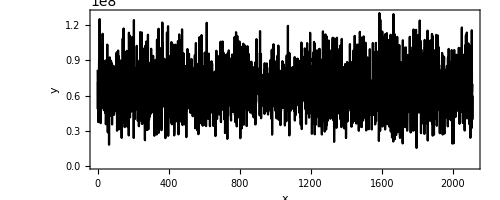

/Capture000001

```mathematica
ListPlot[pydata]
```

```mathematica
Hash["","SHA512","HexString"]
Hash["","SHA256","HexString"]
```

cf83e1357eefb8bdf1542850d66d8007d620e4050b5715dc83f4a921d36ce9ce47d0d13c5d85f2b0ff8318d2877eec2f63b931bd47417a81a538327af927da3e

e3b0c44298fc1c149afbf4c8996fb92427ae41e4649b934ca495991b7852b855

```mathematica
cf83e1357eefb8bdf1542850d66d8007d620e4050b5715dc83f4a921d36ce9ce47d0d13c5d85f2b0ff8318d2877eec2f63b931bd47417a81a538327af927da3e
```